```mathematica
datapathStack = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\Zurich Instruments\\";
datapathStackFolders = FileNames["Board*",datapathStack];
importdataStack = Table[Import[#,"Table"]&/@(FileNames["\\*.txt",datapathStackFolders[[board]]]),{board,1,Dimensions[datapathStackFolders][[1]]}];

datapath = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\MLA Data\\Isolated_Measurements_230202\\";
datapathFolders = FileNames["*",datapath];
importdata = Table[Import[#,"Table"]&/@(FileNames["\\*.txt",datapathFolders[[board]]]),{board,1,Dimensions[datapathFolders][[1]]}];

datapathImpedances = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\MLA Data\\Impedances_Isolated_Cells_230202\\";
importedImpedances = Import[#,"Table"]&/@(FileNames[datapathImpedances<>"*.txt"]);
```

```mathematica
p1=Flatten[Table[{{5-p,5-q,2},{5-p,5-q,1}},{p,1,4},{q,1,4}],2];
p2=Flatten[Table[{{9-p,5-q,2},{9-p,5-q,1}},{p,1,4},{q,1,4}],2];
p3=Flatten[Table[{{4+p,4+q,1},{4+p,4+q,2}},{p,1,4},{q,1,4}],2];
p4=Flatten[Table[{{p,4+q,1},{p,4+q,2}},{p,1,4},{q,1,4}],2];
correspondingNodeCoords=Join[p1,p2,p3,p4];

shuntR = 10.853;
```

# Complete Single Board Measurements

```mathematica
voltage1J = Table[(ToExpression[StringDelete[importdataStack[[board,2*j-1,6+i,2]],","]])*Exp[-I*2π*(ToExpression[importdataStack[[board,2*j-1,6+i,3]]])/360],{board,1,4},{j,1,Dimensions[importdataStack][[2]]/2},{i,1,Length[importdataStack[[1,1,7;;,-1]]]}];

voltage2J = Table[(ToExpression[StringDelete[importdataStack[[board,2*j,6+i,2]],","]])*Exp[-I*2π*(ToExpression[importdataStack[[board,2*j,6+i,3]]])/360],{board,1,4},{j,1,Dimensions[importdataStack][[2]]/2},{i,1,Length[importdataStack[[1,1,7;;,-1]]]}];

frequencies = ToExpression[StringDelete[importdataStack[[1,1,7;;,1]],","]];

impedancesJOrdered = Table[{frequencies[[freq]],(shuntR*(voltage1J[[board,j,freq]]))/(((voltage2J[[board,j,freq]])))},{board,1,4},{j,1,Dimensions[voltage1J][[2]]},{freq,1,Length[importdataStack[[1,1,7;;,-1]]]}];
```

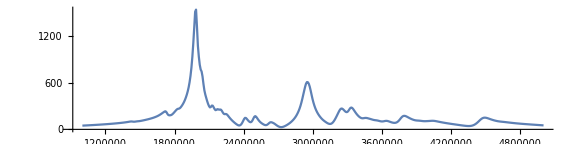

```mathematica
ListLinePlot[Abs[impedancesJOrdered[[4,2]]],PlotRange->All,AspectRatio->1/4,ImageSize->Large]
```

```mathematica
Position[correspondingNodeCoords,{1,1,1}][[1,1]]
```

32

```mathematica
impedances = Table[Abs[impedancesJOrdered[[board,Position[correspondingNodeCoords,{x,y,sub}][[1,1]]]]],{board,1,4},{x,1,8},{y,1,8},{sub,1,2}];
```

```mathematica
impedances//Dimensions
```

{4,8,8,2,500,2}

# Isolated Nodes Measurements

```mathematica
nodes = {{7,1},{6,2},{1,4},{2,4},{4,4},{5,4},{7,4},{8,4},{4,5},{4,6},{4,7},{7,8}};
consideration = {9,10,11};
consideredNodes = nodes[[consideration]];
reordering = {};
shuntR = 10.853;

voltageDataImpedances = Table[importedImpedances[[j,(entry-1)*999+entry*4;;(entry)*999+entry*4]],{j,1,Dimensions[importedImpedances][[1]]},{entry,1,4}];

voltageDataOrdered = Table[importdata[[board,j,(entry-1)*999+entry*4;;(entry)*999+entry*4]],{board,1,Dimensions[importdata][[1]]},{j,1,Dimensions[importdata[[board]]][[1]]},{entry,1,2}];

frequencyArray = voltageDataOrdered[[1,1,1,;;,1]];

ticks = Table[{(Dimensions[frequencyArray][[1]])*i,ToString[i]},{i,1,5}];
```

```mathematica
impedancesIsolated = Table[{frequencyArray[[freq]],(shuntR*(voltageDataImpedances[[j,3,freq,2]])*Exp[I(voltageDataImpedances[[j,4,freq,2]])*2π/360])/(((voltageDataImpedances[[j,1,freq,2]])*Exp[I(voltageDataImpedances[[j,2,freq,2]])*2π/360])-((voltageDataImpedances[[j,3,freq,2]])*Exp[I(voltageDataImpedances[[j,4,freq,2]])*2π/360]))},{j,1,Dimensions[importedImpedances][[1]]},{freq,1,Length[frequencyArray]}];

impedancesIsolatedPlots = Table[ListLinePlot[Abs[impedancesIsolated[[2*(j-1)+sub]]],PlotLabel->"Node: "<>ToString[nodes[[j]]]<>" Sublattice "<>ToString[If[sub==1,"A","B"]],PlotRange->All,AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [MHz]","Res. [Ω]"},Ticks->{ticks,Automatic},PlotLegends->{"Amplitude of impedance spectrum of isolated cells"}],{j,1,Dimensions[importedImpedances][[1]]/2},{sub,1,2}];

impedancesIsolatedPlotsZoomed = Table[ListLinePlot[Abs[impedancesIsolated[[2*(j-1)+sub]]],PlotLabel->"Node: "<>ToString[nodes[[j]]]<>" Sublattice "<>ToString[If[sub==1,"A","B"]],PlotRange->{{1800,3200},{0,Max[Abs[impedancesIsolated[[2*(j-1)+sub,200;;550,2]]]]}},AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [MHz]","Res. [Ω]"},Ticks->{ticks,Automatic},PlotLegends->{"Amplitude of impedance spectrum of isolated cells"}],{j,1,Dimensions[importedImpedances][[1]]/2},{sub,1,2}];
```

```mathematica
Manipulate[impedancesIsolatedPlots[[node,sub]],{node,1,Dimensions[importedImpedances][[1]]/2,1},{sub,1,2,1}]
```

Part::partd: Part specification impedancesIsolatedPlots⟦1,1⟧ is longer than depth of object.

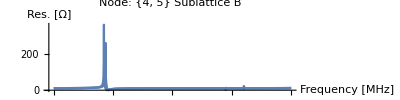

```mathematica
Show[impedancesIsolatedPlots[[9;;11,2]]]
```

```mathematica
overlayIsolatedPlots = Table[ListLinePlot[{Abs[impedancesIsolated[[2*(9-1)+sub]]],Abs[impedancesIsolated[[2*(10-1)+sub]]],Abs[impedancesIsolated[[2*(11-1)+sub]]]},PlotLabel->"Nodes: (4,5),(4,6),(4,7), Sublattice "<>ToString[If[sub==1,"A","B"]],PlotRange->{{900,3000},{0,If[sub==1,75,400]}},AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [MHz]","Res. [Ω]"},Ticks->{ticks,Automatic},PlotLegends->{"(4,5)","(4,6)","(4,7)"}],{sub,1,2}];
```

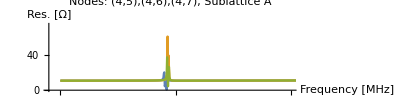

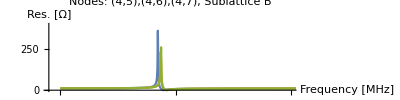

```mathematica
overlayIsolatedPlots[[1]]
overlayIsolatedPlots[[2]]
```

# Comparison

```mathematica
meanIsolated = Table[Mean[Abs[impedancesIsolated[[2*consideration-1+sub,;;,2]]]],{sub,1,2}];
stdIsolated = Table[StandardDeviation[impedancesIsolated[[2*consideration-1+sub,;;,2]]],{sub,1,2}];

normSTDIsolated = stdIsolated/meanIsolated;
aroundNormIsolated = Table[Around[0,normSTDIsolated[[sub,i]]],{sub,1,2},{i,1,Length[normSTDIsolated[[1]]]}];
```

```mathematica
mean = Table[Mean[Table[impedances[[board,node[[1]],node[[2]],sub,;;,2]],{node,consideredNodes}]],{board,1,4},{sub,1,2}];
std = Table[StandardDeviation[Table[impedances[[board,node[[1]],node[[2]],sub,;;,2]],{node,consideredNodes}]],{board,1,4},{sub,1,2}];

normSTD = std/mean;
aroundNorm = Table[Around[0,normSTD[[board,sub,i]]],{board,1,4},{sub,1,2},{i,1,Length[normSTD[[1,1]]]}];
```

```mathematica
aroundNormIsolated//Dimensions
aroundNorm//Dimensions
```

{2,1000}

{4,2,500}

```mathematica
ticks = Table[{(Dimensions[frequencyArray][[1]])/5*i,ToString[i]},{i,1,5}];
ticks2 = Table[{(Dimensions[frequencies][[1]])/5*i,ToString[i]},{i,1,5}];
```

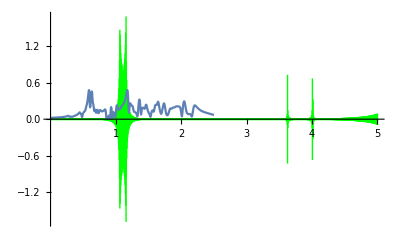

```mathematica
Show[ListLinePlot[aroundNormIsolated[[1]],PlotRange->All,PlotStyle->Green,Ticks->{ticks,Automatic}],ListLinePlot[normSTD[[1,1]],PlotRange->All,Ticks->{ticks2,Automatic}]]
```

```mathematica
p1 =Table[ListLinePlot[aroundNormIsolated[[sub]],PlotRange->{-2.5,2.5},IntervalMarkers->"Bands",IntervalMarkersStyle->Gray,Ticks->{ticks,Automatic},InterpolationOrder->3,AspectRatio->1/4,ImageSize->Full,PlotLegends->Placed[Style["Isolated Nodes, Sub "<>ToString[If[sub==1,A,B]],Gray],{0.35,0}],AxesLabel->{"Frequency [MHz]","Relative Deviation from Respective Mean Value [Arb. Unit]"}],{sub,1,2}];
```

```mathematica
p2 = Table[ListLinePlot[aroundNorm[[board,sub]],PlotRange->{-2.5,2.5},IntervalMarkers->"Bands",IntervalMarkersStyle->Orange,Ticks->{ticks2,Automatic},InterpolationOrder->3,AspectRatio->1/4,ImageSize->Full,PlotLegends->Placed[Style["Selected Nodes Board "<>ToString[board]<>", Sub "<>ToString[If[sub==1,A,B]],Orange],{0.65,0}],AxesLabel->{"Frequency [MHz]","Relative Deviation from Respective Mean Value [Arb. Unit]"}],{board,1,4},{sub,1,2}];
```

```mathematica
Manipulate[Overlay[{p1[[sub]],p2[[board,sub]]}],{board,1,4,1},{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

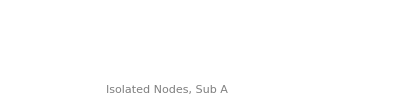
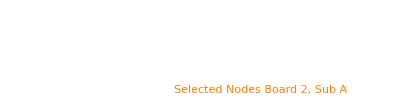

```mathematica
Overlay[{p1[[1]],p2[[2,1]]}]
```